```mathematica
Solve[{0 == x *(1-x) - a1 * x*y/(1 +b1*x), 0 == a1*x*y/(1+b1*x) - a2*y*z/(1+b2*y) - d1*y, 0 == a2*y*z/(1+b2*y) - d2*z}, {x,y,z}]
Solve[0 == x *(1-x) - a1 * x*y/(1 +b1*x), x]
```

{{x→0,y→-d2/(-a2+b2 d2),z→-d1/(a2-b2 d2)},{x→1,y→0,z→0},{x→-d1/(-a1+b1 d1),y→(a1-d1-b1 d1)/(a1-b1 d1)^2,z→0},{x→(-a2+a2 b1+b2 d2-b1 b2 d2-√(-4 (-a2+a1 d2+b2 d2) (a2 b1-b1 b2 d2)+(a2-a2 b1-b2 d2+b1 b2 d2)^2))/(2 (a2 b1-b1 b2 d2)),y→-d2/(-a2+b2 d2),z→1/(a2 b1 d2-b1 b2 d2^2)(-a2+a1 d2+b2 d2-b1 d1 d2-a2^2/(2 (a2 b1-b1 b2 d2))+(a2^2 b1)/(2 (a2 b1-b1 b2 d2))+(a2 b2 d2)/(a2 b1-b1 b2 d2)-(a2 b1 b2 d2)/(a2 b1-b1 b2 d2)-(b2^2 d2^2)/(2 (a2 b1-b1 b2 d2))+(b1 b2^2 d2^2)/(2 (a2 b1-b1 b2 d2))-(a2 √(-4 (-a2+a1 d2+b2 d2) (a2 b1-b1 b2 d2)+(a2-a2 b1-b2 d2+b1 b2 d2)^2))/(2 (a2 b1-b1 b2 d2))+(b2 d2 √(-4 (-a2+a1 d2+b2 d2) (a2 b1-b1 b2 d2)+(a2-a2 b1-b2 d2+b1 b2 d2)^2))/(2 (a2 b1-b1 b2 d2)))},{x→(-a2+a2 b1+b2 d2-b1 b2 d2+√(-4 (-a2+a1 d2+b2 d2) (a2 b1-b1 b2 d2)+(a2-a2 b1-b2 d2+b1 b2 d2)^2))/(2 (a2 b1-b1 b2 d2)),y→-d2/(-a2+b2 d2),z→1/(a2 b1 d2-b1 b2 d2^2)(-a2+a1 d2+b2 d2-b1 d1 d2-a2^2/(2 (a2 b1-b1 b2 d2))+(a2^2 b1)/(2 (a2 b1-b1 b2 d2))+(a2 b2 d2)/(a2 b1-b1 b2 d2)-(a2 b1 b2 d2)/(a2 b1-b1 b2 d2)-(b2^2 d2^2)/(2 (a2 b1-b1 b2 d2))+(b1 b2^2 d2^2)/(2 (a2 b1-b1 b2 d2))+(a2 √(-4 (-a2+a1 d2+b2 d2) (a2 b1-b1 b2 d2)+(a2-a2 b1-b2 d2+b1 b2 d2)^2))/(2 (a2 b1-b1 b2 d2))-(b2 d2 √(-4 (-a2+a1 d2+b2 d2) (a2 b1-b1 b2 d2)+(a2-a2 b1-b2 d2+b1 b2 d2)^2))/(2 (a2 b1-b1 b2 d2)))},{x→0,y→0,z→0}}

```mathematica
{{x->0},{x->(-1+b1-√(1+2 b1+b1^2-4 a1 b1 y))/(2 b1)},{x->(-1+b1+√(1+2 b1+b1^2-4 a1 b1 y))/(2 b1)}}
```

```mathematica
Plot[(-1+b1-√(1+2 b1+b1^2-4 a1 b1 y))/(2 b1),y]
```

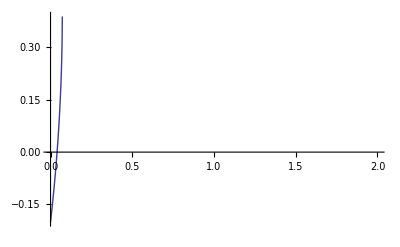

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→0.,y→0.2,z→-316.667},{x→0.345455,y→0.071405,z→0.},{x→0.4-0.8 ⅈ,y→0.2,z→123.333-80. ⅈ},{x→0.4+0.8 ⅈ,y→0.2,z→123.333+80. ⅈ},{x→1.,y→0.,z→0.},{x→0.,y→0.,z→0.}}

```mathematica
a1 := 25
a2 := 0.1
b1 := 5
b2 := 45
d1 := 25/6 - 1
d2 := 0.002
Plot[(-1+b1-√(1+2 b1+b1^2-4 a1 b1 y))/(2 b1),{y,0,2}]
Solve[{0 == x*(1-x) - a1*x*y/(1+b1*x), 0 == a1*x*y/(1+b1*x) - a2*y*z/(1 + b2*y) - d1*y, 0 ==  a2*y*z/(1 + b2*y)  - d2*z},{x,y,z}]
```

```mathematica
x:= -d1/(-a1+b1 d1)
y:=(a1-d1-b1 d1)/(a1-b1 d1)^2
M = {{1 - 2x - a1*y/(1+b1*x)^2, - a1*x/(1+b1*x)},{a1*y/(1+b1*x)^2,a1*x/(1+b1*x) - d1}}
Eigenvalues[M]
(*{vals, vecs} = Eigensystem[M]*)
```

{{1+(2 d1)/(-a1+b1 d1)-(a1 (a1-d1-b1 d1))/((a1-b1 d1)^2 (1-(b1 d1)/(-a1+b1 d1))^2),(a1 d1)/((-a1+b1 d1) (1-(b1 d1)/(-a1+b1 d1)))},{(a1 (a1-d1-b1 d1))/((a1-b1 d1)^2 (1-(b1 d1)/(-a1+b1 d1))^2),-d1-(a1 d1)/((-a1+b1 d1) (1-(b1 d1)/(-a1+b1 d1)))}}

{1/(2 (a1^2-a1 b1 d1))(-a1 d1+a1 b1 d1-b1 d1^2-b1^2 d1^2-√((a1 d1-a1 b1 d1+b1 d1^2+b1^2 d1^2)^2-4 (a1^2-a1 b1 d1) (a1^2 d1-a1 d1^2-2 a1 b1 d1^2+b1 d1^3+b1^2 d1^3))),1/(2 (a1^2-a1 b1 d1))(-a1 d1+a1 b1 d1-b1 d1^2-b1^2 d1^2+√((a1 d1-a1 b1 d1+b1 d1^2+b1^2 d1^2)^2-4 (a1^2-a1 b1 d1) (a1^2 d1-a1 d1^2-2 a1 b1 d1^2+b1 d1^3+b1^2 d1^3)))}

```mathematica
a[x_,y_] := x*(1-x) - (a1*x*y)/(1 + b1*x)
b[x_,y_,z_] := (a1*x*y)/(1 + b1*x) - (a2*y*z)/(1 + b2*y) - d1*y
c[y_,z_] := (a2*y*z)/(1+b2*y) - d2*z
dera[x_,y_] := D[a[x,y],x]
derb[x_,y_,z_] := D[b[x,y,z],y]
derc[y_,z_] := D[c[y,z],z]
dera[x,y]*a[x,y]^3-dera[x,y]*a[x,y]^2 -dera[x,y] + a[x,y]* dera[x,y]+b[x,y,z]* derb[x,y,z]+c[y,z]* derc[y,z]
 -dera[x,y] + a[x,y]* dera[x,y]+b[x,y,z]* derb[x,y,z]+c[y,z]* derc[y,z]
```

-1+2 x-(5 x y)/(1+5 x)^2+y/(1+5 x)+(1-2 x+(5 x y)/(1+5 x)^2-y/(1+5 x)) ((1-x) x-(x y)/(1+5 x))-(1-2 x+(5 x y)/(1+5 x)^2-y/(1+5 x)) ((1-x) x-(x y)/(1+5 x))^2+(1-2 x+(5 x y)/(1+5 x)^2-y/(1+5 x)) ((1-x) x-(x y)/(1+5 x))^3+(-0.004+x/(1+5 x)+(4.5 y z)/(1+45 y)^2-(0.1 z)/(1+45 y)) (-0.004 y+(x y)/(1+5 x)-(0.1 y z)/(1+45 y))+(-0.002+(0.1 y)/(1+45 y)) (-0.002 z+(0.1 y z)/(1+45 y))

-1+2 x-(5 x y)/(1+5 x)^2+y/(1+5 x)+(1-2 x+(5 x y)/(1+5 x)^2-y/(1+5 x)) ((1-x) x-(x y)/(1+5 x))+(-0.004+x/(1+5 x)+(4.5 y z)/(1+45 y)^2-(0.1 z)/(1+45 y)) (-0.004 y+(x y)/(1+5 x)-(0.1 y z)/(1+45 y))+(-0.002+(0.1 y)/(1+45 y)) (-0.002 z+(0.1 y z)/(1+45 y))

```mathematica
Jacob := {{1 - 2x - a1*y/(1 + b1*x)^2, - (a1*x)/(1+b1*x), 0},{a1*y/(1+b1*x)^2, a1*x/(1+b1*x) - a2*x/(1+b2*y)^2-d1,-a2*y/(1+b2*y)},{0,a2*z/(1+b2*y)^2,a2*y/(1+b2*y)-d2}}
```